2.1 Index of fixed point

a)

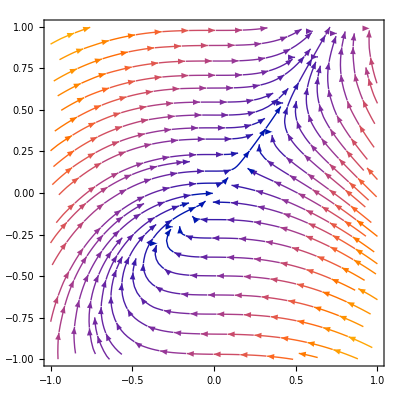

```mathematica
xdot =.;ydot=.;y=.;x=.;P=.;lim=.;
xdot = y-x;
ydot = x^2;
P ={xdot,ydot};
lim = 1;
StreamPlot[P,{ x,-lim,lim},{y,-lim,lim}]
```

b)

r Cos[theta] (Sin[theta]+Cos[theta] (-1+r Sin[theta]))

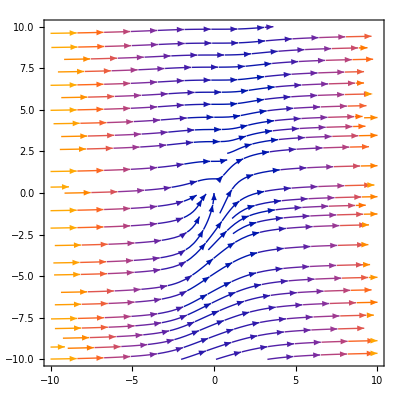

```mathematica
xdot =.;ydot=.;y=.;x=.;P=.;lim=.; theta=.;
lim = 10;
xdot = y-x;
ydot = x^2;
P ={xdot,ydot};
P =ToPolarCoordinates[{P}];
StreamPlot[P,{x,-lim,lim},{y,-lim,lim}]
```

c)

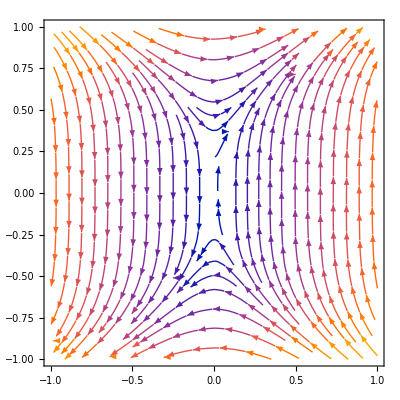

```mathematica
xdot =.;ydot=.;y=.;x=.;P=.;lim=.;
xdot = y^3;
ydot = x;
P ={xdot,ydot};
lim = 1/1;
StreamPlot[P,{ x,-lim,lim},{y,-lim,lim}]
```

d)

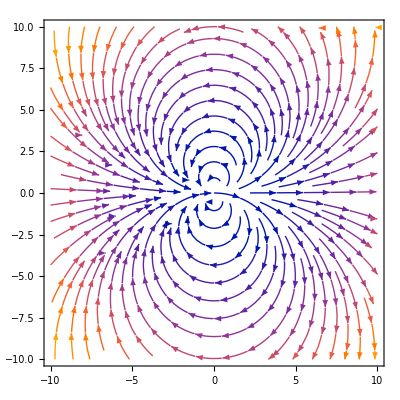

```mathematica
xdot =.;ydot=.;y=.;x=.;P=.;lim=.;
n=.;
xdot =(x^2+y^2)^(Abs[n]/2)*Cos[n*ArcTan[y/x]] ;
ydot = (x^2+y^2)^(Abs[n]/2)*Sin[n*ArcTan[y/x]];
lim = 10;
n=2;

P ={xdot,ydot};
StreamPlot[{(x^2+y^2)^(Abs[n]/2)*Cos[n*ArcTan[y/x]],(x^2+y^2)^(Abs[n]/2)*Sin[n*ArcTan[y/x]]},{x,-lim,lim},{y,-lim,lim}]
```

2.2e

```mathematica
y=.;x=.;sigma=.;t=.;sigma=2;ClearAll[y];ClearAll[x];
s=NDSolve[{x'[t]==y[t],y'[t]==-Sin[x[t]]-sigma*y[t],x[0]==y[0]==0},{x[t],y[t]},{t,0,10}]
lim=Pi;
Manipulate[StreamPlot[{y,-Sin[x]-a*y},{x,-lim+Pi/2,lim+Pi/2},{y, -lim,lim}],{a,0,3}];

sigma=.;
M = {{0 , 1},{-Cos[x], -sigma}};
x=0;
lambda1 =Eigenvalues[M]
x=Pi;
lambda2 = Eigenvalues[M]
```

{{x[t]→InterpolatingFunction[…][t],y[t]→InterpolatingFunction[…][t]}}

{1/2 (-sigma-√(-4+sigma^2)),1/2 (-sigma+√(-4+sigma^2))}

{1/2 (-sigma-√(4+sigma^2)),1/2 (-sigma+√(4+sigma^2))}

2.3

```mathematica
xdot=.;ydot=.;y=.;x=.;sigma=.;mu=.;xdot2=.;ydot2=.;
t=.;v=.;u=.;

mu=0;
x0={v};
y0={u};
(*NDSolve[{x'[t]==-{5,-1}*y[t]+{-x[t]^3,3*y[t]^3}, y'[t]=={5,-1}*x[t] + {-x[t]^2,2*x[t]^2}, x[0]==x0,y[0]==y0},{x,y},{t}]*)
```

NDSolve::ndlim: Range specification t is not of the form {x, xend} or {x, xmin, xmax}.

NDSolve::ndinnt: Initial condition {v} is not a number or a rectangular array of numbers.

NDSolve[{x'[t]=={-x[t]^3-5 y[t],y[t]+3 y[t]^3},y'[t]=={5 x[t]-x[t]^2,-x[t]+2 x[t]^2},x[0]=={v},y[0]=={u}},{x,y},{t}]

2.4
a)

```mathematica
xdot = .;ydot = .;x=.;y=.;
lim=1/2;
Manipulate[StreamPlot[{mu x + y -x^2,-x+y mu + 2x^2},{x,-lim,lim+1/10},{y,-lim,lim}], {mu,-1,.1}]
```

1/2

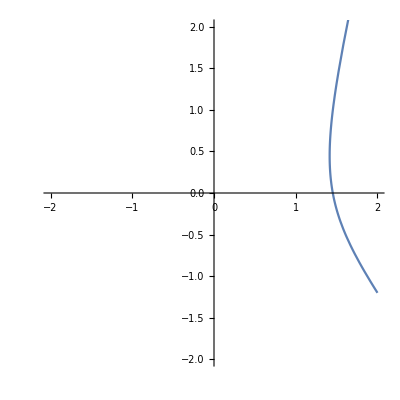

```mathematica
minx=-2;
miny=-2;
maxx=2;
maxy=2;
mu=1.1;
sol[x0_,y0_]:=NDSolve[{x'[t]==mu x[t] + y[t] -x[t]^2,y'[t]==-x[t]+y[t]* mu + 2x[t]^2,x[0]==x0,y[0]==y0},{x,y},{t,0,10}]
initialC=Join[Table[{minx,y},{y,miny,maxy,0.1}],Table[{maxx,y},{y,miny,maxy,0.1}],Table[{x,miny},{x,minx,maxx,0.1}],Table[{x,maxy},{x,minx,maxx,0.1}]];
ParametricPlot[Evaluate[{x[t],y[t]}/. sol[initialC[[50,1]],initialC[[50,2]]]],{t,0,6},PlotRange->{{minx,maxx},{miny,maxy}}]
```

2.4
a)

```mathematica
x=.;y=.;μ=.;Remove[flow];Remove[sol];
flow = {μ*x+y-x^2, -x+μ*y+2x^2};
fpsols = Solve[flow==0,{x,y}];
stabmat = D[flow,{{x,y}}]/.%[[2]];
stabmat//MatrixForm;
eigsys = Eigensystem[stabmat];
eigenVal = Eigenvalues[stabmat]
unstabexponent = eigsys[[1,2]];
unstabdirection = eigsys[[2,2]];
```

{(-1+2 μ-√(5+9 μ^2+4 μ^3+μ^4))/(2+μ),(-1+2 μ+√(5+9 μ^2+4 μ^3+μ^4))/(2+μ)}

```mathematica
dynsys = {x'[t]== μ*x[t]+y[t]-x[t]^2,y'[t]==-x[t]+μ*y[t]+2x[t]^2};
sol[μdummy_,T_]:=Quiet@NDSolve[Join[dynsys,Thread[{x[0],y[0]}=={(1+μ^2)/(2+μ),(1-2 μ+μ^2-2 μ^3)/(2+μ)^2}-0.001*unstabdirection]]/.μ->μdummy,{x[t],y[t]},{t,0,T}];
```

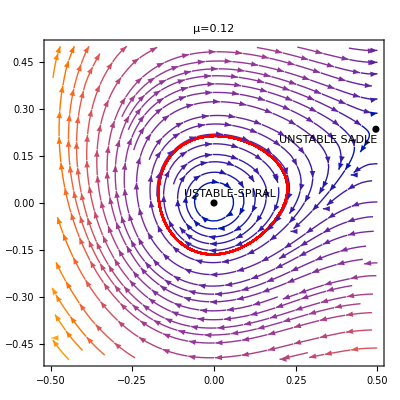

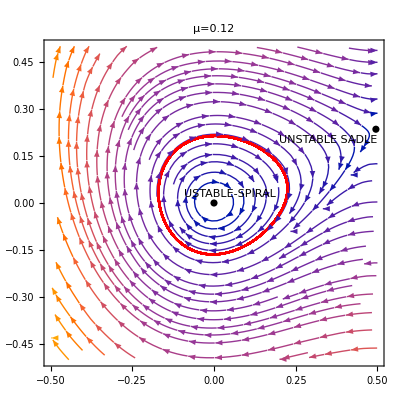

```mathematica
μval = 0.02;
Tmin=800;
Tmax = 1000;
text1 = Graphics[Text["", {-0.4,-0.55}]];
text2 = Graphics[Text["UNSTABLE SADLE", {0.35, 0.2}]];
text3 = Graphics[Text["USTABLE-SPIRAL", {0.05,0.03}]];
text4 = Graphics[Text["", {0.05, 0.4}]];
p =Show[StreamPlot[flow/.μ->μval,{x,-0.5,0.5},{y,-0.5,0.5}],ParametricPlot[Evaluate[{x[t],y[t]}/.sol[μval,Tmax]],{t,Tmin,Tmax},PlotStyle->Red,PlotRange->{{-0.5,2.5},{-0.5,6.5}}], ListPlot[{x,y}/.fpsols/.μ->μval,PlotRange->{{-1.5,1.5},{-1.5,1.5}},PlotStyle->Black], text1, text2, text3, text4,PlotLabel->"μ=0.12"]
(p//Normal)/.Line[x_]:>{Arrowheads[{0.05,0.05,0.05}],Arrow[x]}
```

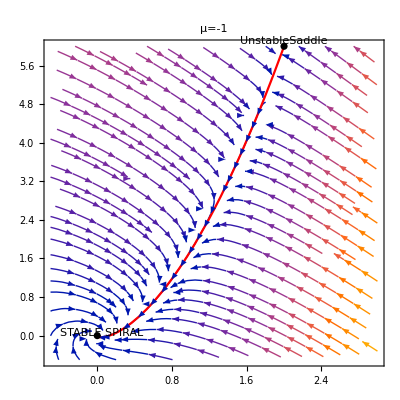

2.4 b)

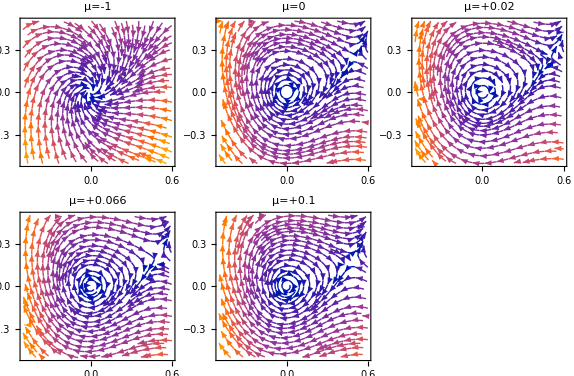

```mathematica
xdot = .;ydot = .;x=.;y=.;
lim=1/2;
Remove[p1]
Remove[p2]
Remove[p3]
Remove[p4]
Remove[p5]

mu = -1;
p1 = StreamPlot[{mu x + y -x^2,-x+y mu + 2x^2},{x,-lim,lim+1/10},{y,-lim,lim},PlotLabel->"μ="+mu];
mu=0;
p2 = StreamPlot[{mu x + y -x^2,-x+y mu + 2x^2},{x,-lim,lim+1/10},{y,-lim,lim},PlotLabel->"μ=0"];
mu=0.02;
p3 = StreamPlot[{mu x + y -x^2,-x+y mu + 2x^2},{x,-lim,lim+1/10},{y,-lim,lim},PlotLabel->"μ="+mu];
mu=0.066;
p4 = StreamPlot[{mu x + y -x^2,-x+y mu + 2x^2},{x,-lim,lim+1/10},{y,-lim,lim},PlotLabel->"μ="+mu];
mu=0.1;
p5 = StreamPlot[{mu x + y -x^2,-x+y mu + 2x^2},{x,-lim,lim+1/10},{y,-lim,lim},PlotLabel->"μ="+mu];
GraphicsGrid[{{p1,p2,p3},{p4,p5}}]
```

2.4 d)

```mathematica
x=.;y=.;μ=.;Remove[flow];Remove[sol];
flow = {μ*x+y-x^2, -x+μ*y+2x^2};
fpsols = Solve[flow==0,{x,y}];
stabmat = D[flow,{{x,y}}]/.%[[2]];
stabmat//MatrixForm;

(* Unstable is + Sqrt *)
eigenVal = Eigenvalues[stabmat][[2]]
```

(-1+2 μ+√(5+9 μ^2+4 μ^3+μ^4))/(2+μ)

2.4 e)

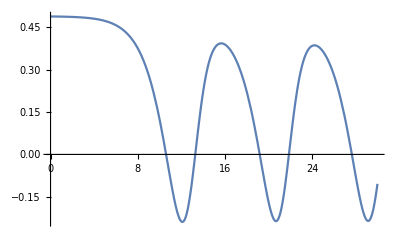

```mathematica
x=.;y=.;
lim=1/2;
mu = 0.05;
StreamPlot[{mu x + y -x^2,-x+y mu + 2x^2},{x,-lim,lim+1/10},{y,-lim,lim}];
dynsys = {x'[t]== μ*x[t]+y[t]-x[t]^2,y'[t]==-x[t]+μ*y[t]+2x[t]^2};
sol[μdummy_,T_]:=Quiet@NDSolve[Join[dynsys,Thread[{x[0],y[0]}=={(1+μ^2)/(2+μ),(1-2 μ+μ^2-2 μ^3)/(2+μ)^2}-0.001*unstabdirection]]/.μ->μdummy,{x[t],y[t]},{t,0,T}];
μval = 0.05;
Tmin=0;
Tmax = 100;
text1 = Graphics[Text["", {-0.4,-0.55}]];
text2 = Graphics[Text["", {0.35, 0.2}]];
text3 = Graphics[Text["", {0.05,0.03}]];
text4 = Graphics[Text["", {0.05, 0.4}]];
p =Show[StreamPlot[flow/.μ->μval,{x,-0.5,0.5},{y,-0.5,0.5}],ParametricPlot[Evaluate[{x[t],y[t]}/.sol[μval,Tmax]],{t,Tmin,Tmax},PlotStyle->Red,PlotRange->{{-0.5,2.5},{-0.5,6.5}}], ListPlot[{x,y}/.fpsols/.μ->μval,PlotRange->{{-1.5,1.5},{-1.5,1.5}},PlotStyle->Black], text1, text2, text3, text4,PlotLabel->"μ=0.12"];
(p//Normal)/.Line[x_]:>{Arrowheads[{0.05,0.05,0.05}],Arrow[x]};

a=.;
a = Evaluate[{x[t],y[t]}/.sol[μval,Tmax]];
Plot[a[[1,1]],{t,0,30}]
```